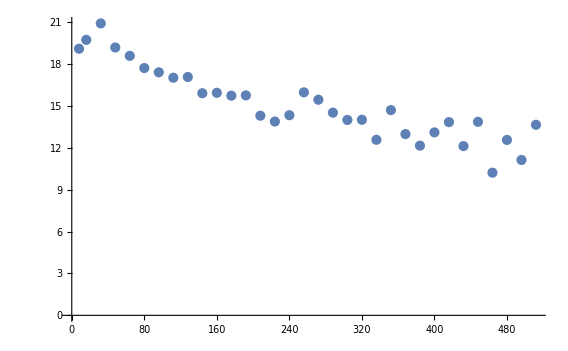

```mathematica
ListPlot[Callout[#,#]&/@({#[[1]],Log2[#[[2]]]}&/@{{8,569450},{16,884680},{32,2006191},{48,605195},{64,399429},{80,218237},{96,176408},{112,134652},{128,139622},{144,62300},{160,63658},{176,55235},{192,55954},{208,20408},{224,15249},{240,20919},{256,65133},{272,45155},{288,23740},{304,16503},{320,16656},{336,6163},{352,26964},{368,8181},{384,4599},{400,8897},{416,14815},{432,4499},{448,15035},{464,1201},{480,6117},{496,2260},{512,12996}})]
```

```mathematica
Table[{Max[sz,8],Floor[4096/Max[sz,8]]},{sz,0,512,16}]//MatrixForm
```

(8 | 512
16 | 256
32 | 128
48 | 85
64 | 64
80 | 51
96 | 42
112 | 36
128 | 32
144 | 28
160 | 25
176 | 23
192 | 21
208 | 19
224 | 18
240 | 17
256 | 16
272 | 15
288 | 14
304 | 13
320 | 12
336 | 12
352 | 11
368 | 11
384 | 10
400 | 10
416 | 9
432 | 9
448 | 9
464 | 8
480 | 8
496 | 8
512 | 8)